```mathematica
(* Final *)
```

```mathematica
(* Step 1
Practicing visualization 
*)

(* MIT Sloan Data *)
(* Explain Data *)
path=NotebookDirectory[]
```

C:\Users\User 1\Documents\Final-Project-Kacham\

```mathematica
dataset1 = Import[path<>"NexGen13newPlays.xlsx"]
```

{{{Play Id, X Position, Y Position, Possession Id, Distance, Vertical Distance, Total Distance, Thrower id, Reciever Id,11, Point Id, Game Id, Opponent Name, Last X, Last Y, Next X, Next Y, Home on Offense},2808,{1}}}
 |  |  |  |

```mathematica
keys=dataset1[[1,1]]
```

{Play Id, X Position, Y Position, Possession Id, Distance, Vertical Distance, Total Distance, Thrower id, Reciever Id, Breakthrow?, Stall Six?, Stall Eight?, Defender Id, Stall?, Block?, Throwaway?, Intercept?, Drop?, Score?, Home Attacking Right?, Point Id, Game Id, Opponent Name, Last X, Last Y, Next X, Next Y, Home on Offense}

```mathematica
papersummary= Dataset[Map[Association[Thread[Rule[keys,#]]]&,dataset1[[1,2;;Length[dataset1[[1]]]]]]]
```

Dataset[<>]

```mathematica
papersummarychangeddata= papersummary[All,{5->(Quantity[#,"Feet"]&)}][All,{6->(Quantity[#,"Feet"]&)}][All,{7->(Quantity[#,"Feet"]&)}]
```

Dataset[<>]

```mathematica
datasetxy = papersummarychangeddata[All,{2,3}]
```

Dataset[<>]

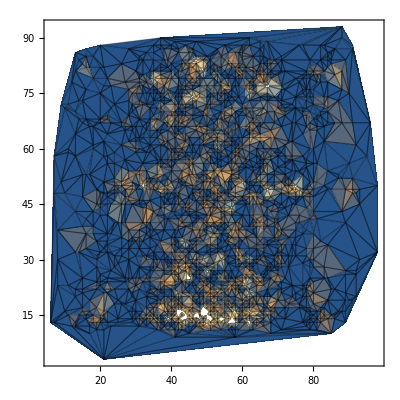

```mathematica
ListDensityPlot[Counts[Round[Normal@Values[datasetxy]/100]],Mesh->All]
```

```mathematica
datasetDistance= papersummarychangeddata[All,{5,6}]
```

Dataset[<>]

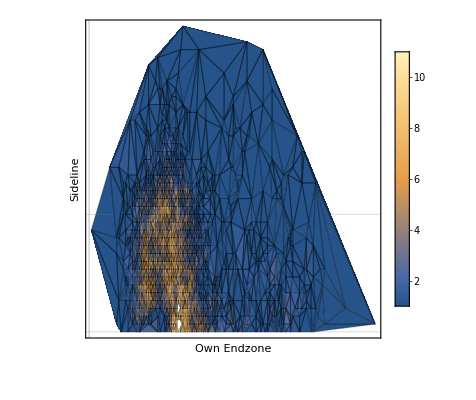

```mathematica
ListDensityPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],Mesh->All,PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"},FrameTicks->{None,None},GridLines->{{-30,-30},{0,15}}]
(* This is showing probability of scoring as a function of field position *)
```

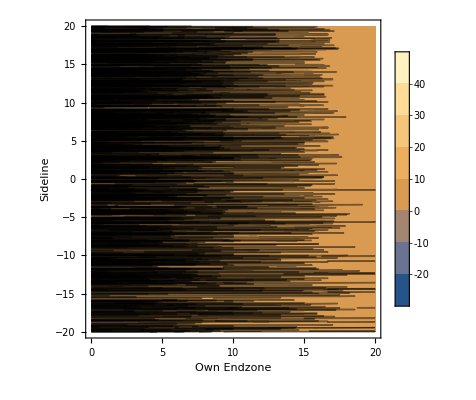

```mathematica
(* Plots that dont actually make sense but look cool *)
(* ask Carlo if it's cat vomit *)
ListContourPlot[Map[Log,#]&/@Counts[Round[Normal@Values[datasetDistance]]],PlotLegends->Automatic, FrameLabel-> {"Own Endzone", "Sideline"},DataRange-> {{20,0},{-20,20}}]
```

```mathematica
(* Step 2 *)
(* Adding Ultimate Frisbee Raw Data to the Wolfram Data Repository and representing raw data *)
(* Website: Ultianalytics *)
(* Scrape raw data for all featured AUDL teams 2014 - 2017 *)
```

```mathematica
html=Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\mainpage.txt","Text"]; (* Ultianalytics Home Page *)
```

```mathematica
names={"Chicago Wildfire","Cincinnati Revolution","DC Breeze","Detroit Mechanix","Indianapolis AlleyCats","Madison Radicals","Minnesota Wind Chill","Montreal Royal","New York Empire","Philadelphia Phoenix","Rochester Dragons","Salt Lake Lions","San Francisco FlameThrowers","San Jose Spiders","Seattle Raptors","Toronto Rush","Vancouver Riptide","Atlanta Hustle","Charlotte Express","Chicago Wildfire","Cincinnati Revolution","DC Breeze","Detroit Mechanix","Indianapolis AlleyCats","Jacksonville Cannons","Los Angeles Aviators","Madison Radicals ","Minnesota Wind Chill ","Montreal Royal","Nashville Nightwatch","New York Empire","Ottawa Outlaws ","Philadelphia Phoenix","Pittsburgh Thunderbirds","Raleigh Flyers ","Rochester Dragons","San Diego Growlers","San Francisco FlameThrowers","San Jose Spiders","Seattle Cascades","Toronto Rush ","Vancouver Riptide","Atlanta Hustle","Austin Sol","Charlotte Express","Chicago Wildfire","Cincinnati Revolution","DC Breeze","Dallas Roughnecks","Detroit Mechanix","Indianapolis AlleyCats","Jacksonville Cannons","Los Angeles Aviators","Madison Radicals ","Minnesota Wind Chill ","Montreal Royal","Nashville Nightwatch","New York Empire","Ottawa Outlaws ","Philadelphia Phoenix","Pittsburgh Thunderbirds","Raleigh Flyers ","San Diego Growlers","San Francisco FlameThrowers","San Jose Spiders","Seattle Cascades","Toronto Rush ","Vancouver Riptide","Atlanta Hustle","Austin Sol","Chicago Wildfire","DC Breeze","Dallas Roughnecks","Detroit Mechanix","Indianapolis AlleyCats","Jacksonville Cannons","Los Angeles Aviators","Madison Radicals ","Minnesota Wind Chill ","Montreal Royal","Nashville Nightwatch","New York Empire","Ottawa Outlaws ","Philadelphia Phoenix","Pittsburgh Thunderbirds","Raleigh Flyers ","San Diego Growlers","San Francisco FlameThrowers","San Jose Spiders","Seattle Cascades","Toronto Rush ","Vancouver Riptide"};
```

```mathematica
keys={"Date/Time","Tournamemnt","Opponent","Point Elapsed Seconds","Line","Our Score - End of Point","Their Score - End of Point","Event Type","Action","Passer","Receiver","Defender","Hang Time (secs)","Player 0","Player 1","Player 2","Player 3","Player 4","Player 5","Player 6","Player 7","Player 8","Player 9","Player 10","Player 11","Player 12","Player 13","Player 14","Player 15","Player 16","Player 17","Player 18","Player 19","Player 20","Player 21","Player 22","Player 23","Player 24","Player 25","Player 26","Player 27","Elapsed Time (secs)"};
```

```mathematica
ids={"5762298832486400","5199348879065088","5104011879383040","5634601401712640","5688687119564800","5173627930542080","5646521009700864","5672188833169408","5719707252424704","5701394610782208","5658753101725696","5736577883963392","5672878150254592","5767202099691520","5700228501995520","5666961832804352","5721191432060928","5740216795004928","5712818124881920","5654595548217344","5655358173347840","5753798823772160","5707300165648384","5711261467672576","5664284977659904","5128666635829248","5640136574369792","5691616589250560","5069252692279296","5705148370255872","5206956054675456","5769906008096768","5201331526565888","5723974822526976","4919856549855232","5114556594520064","5142198416834560","5686487861428224","5749730717990912","5632202645700608","5153306812874752","5675918433452032","5758196635402240","5199033182191616","5664810037411840","5743365039587328","5716256766296064","4860723440123904","5764281479987200","6327231433408512","5708939920408576","5643517367943168","5671536392404992","5674069752020992","5635093192245248","5738275486564352","5724822843686912","5633494390669312","5118639615246336","5070544437248000","5683257223938048","5753050442498048","5705718560718848","5704221898833920","5751646390845440","5641462360309760","5651757665353728","5684793748488192","5670377556541440","5734743547052032","5758048710688768","5722152447770624","5681589568667648","5754980359208960","5701751084679168","5471866718257152","5732910535540736","4868028676177920","5684961520648192","5075454121738240","5182111044599808","5638404075159552","5753341694967808","6220853180104704","5663684521099264","5682238511382528","5662069344960512","5094953273262080","6597766625099776","5648334039547904","5131065358286848","6226234774126592"};
```

```mathematica
teams=StringCases[html,"<a href=\"app/#/"~~x:Shortest[__]~~"/players\">"~~y:Shortest[__]~~"</a>":>{x,y}];
```

```mathematica
importTeam[{id_,name_}]:=Module[{data,keys},
data=Import["http://www.ultianalytics.com/rest/view/team/"<>id<>"/stats/export"];
keys=data⟦1⟧;
Dataset[Association[Thread[keys⟦;;Min[Length[#],52]⟧->#⟦;;Min[Length[#],52]⟧]]&/@Drop[data,1]][All,<|"ID"->id,"Name"->name,#|>&]
]
```

```mathematica
i=0;
SetSharedVariable[i];
PrintTemporary[Dynamic[{ProgressIndicator[i/Length[teams]],i}]];
teamDatasets=ParallelMap[(PrintTemporary[++i];importTeam[#])&,teams];
CloseKernels[];
```

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
allData=Join@@teamDatasets
```

Dataset[<>]

```mathematica
DumpSave["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\data\\dataset.mx",allData];
```

```mathematica
Get["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\data\\dataset.mx"];
```

```mathematica
(* Check if all good *)
```

```mathematica
FirstPosition[Normal@allData,_?(Length[#]>50&)]
```

{33663}

```mathematica
allDataUniform=allData[All,If[Length[#]==54,#,Join[#,<|"Absolute Distance"->Missing[],"Begin Area"->Missing[],"Begin X"->Missing[],"Begin Y"->Missing[],"Distance Unit of Measure"->Missing[],"End Area"->Missing[],"End X"->Missing[],"End Y"->Missing[],"Lateral Distance"->Missing[],"Toward Our Goal Distance"->Missing[]|>]]&]
```

Dataset[<>]

```mathematica
curatedData=
allDataUniform[All,{"Date/Time"->DateObject,"Point Elapsed Seconds"->(Quantity[#,"Seconds"]&),"Absolute Distance"->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Lateral Distance" ->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Hang Time (secs)"->(Quantity[#,"Seconds"]&),"Toward Our Goal Distance"->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Elapsed Time (secs)"->(Quantity[#,"Seconds"]&)}];
```

```mathematica
datasetulti= KeyDrop[curatedData,"Distance Unit of Measure"];
```

```mathematica
DumpSave["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\datasetulti.mx",datasetulti];
```

```mathematica
(* Compare some data *)
```

```mathematica
(* Comparing Point Elapsed Seconds 2014 - 2017 teams *)
(* What does that mean: *)
```

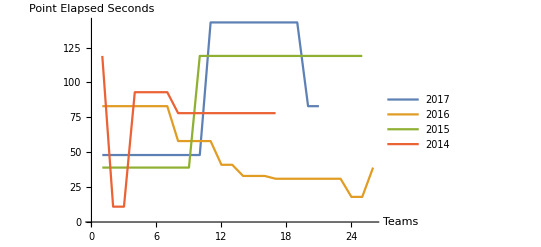

```mathematica
data1 = datasetulti[4 ;;24,6];
data2 = datasetulti[25 ;; 50,6];
data3 = datasetulti[51;; 75,6];
data4 = datasetulti[76;; 92,6];
ListLinePlot[{data1, data2,data3,data4},PlotLegends->{"2017","2016","2015","2014"},AxesLabel->{"Teams","Point Elapsed Seconds"}]
```

```mathematica
(* Filled out the data repository form, got ap ublisher id, waiting for approval *)
```

```mathematica
(* Step 3 *)
(* UltiAnalytics Summary Data AUDL teams 2017 *)
```

```mathematica
(* Goal - Help people understand Ultimate Frisbee tactics and work more with visualization *)
```

```mathematica
path=NotebookDirectory[]
```

C:\Users\User 1\Documents\Final-Project-Kacham\

```mathematica
rawdata=Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\Ulti Analytics Summary Stats\\SummaryStatsAllTeams.xlsx","Data"]
```

{{{Year,Team,Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,10,Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls},822}}
 |  |  |  |

```mathematica
keys=rawdata[[1,1]]
```

{Year,Team,Player,+/-,Games played,Points played,Minutes played,O-line points played,+/- O-line,D-line points played,+/- D-line,Touches,Goals,Callahans,Assists,Throws,Throw aways,Stalled's,Passer Penalties (turnovers),Callahaned's (other team scored),Throw %,Catches,Drops,Catch %,Ds,Pulls,Avg Pull Hang Time,OB Pulls}

```mathematica
teamssummary2017= Dataset[Map[Association[Thread[Rule[keys,#]]]&,rawdata[[1,2;;Length[rawdata[[1]]]]]]]
```

Dataset[<>]

```mathematica
teamssummary2017set2 = teamssummary2017[All,{21->(Quantity[#,"Percent"]&)}][All,{24->(Quantity[#,"Percent"]&)}][All,{27 ->( Quantity[#,"Seconds"]&)}]
```

Dataset[<>]

```mathematica
totalPointsPlayedAllTeams = Total[teamssummary2017[All,If[!NumberQ[#["Points played"]],0,#["Points played"]]&]]
```

93293.5

```mathematica
totalOLine = Total[teamssummary2017[All,If[!NumberQ[#["O-line points played"]],0,#["O-line points played"]]&]]
```

46547.

```mathematica
totalDLine = Total[teamssummary2017[All,If[!NumberQ[#["D-line points played"]],0,#["D-line points played"]]&]]
```

46746.5

```mathematica
(* Comparing O-line points played to D-line points played *)
```

```mathematica
datasetcompare1 =teamssummary2017[All,{8,10}]
```

Dataset[<>]

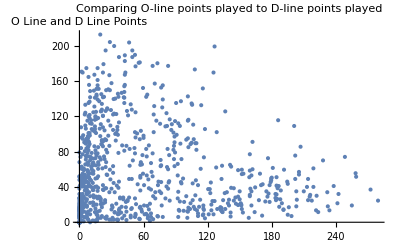

```mathematica
ListPlot[teamssummary2017[[All,{8,10}]],Axes->{True,True},Ticks->{None,Automatic},AxesLabel->{None,HoldForm["O Line and D Line Points"]},PlotLabel->"Comparing O-line points played to D-line points played"]
```

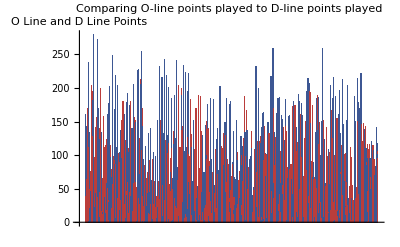

```mathematica
BarChart[datasetcompare1,ChartStyle->"DarkRainbow",Axes->{False,True},PlotLabel->"Comparing O-line points played to D-line points played",Ticks->{None,Automatic},AxesLabel->{None,HoldForm["O Line and D Line Points"]}]
```

```mathematica
(* Takeaway: there are more D-Line points played then O-line points *)
```

```mathematica
(* Comparing throwing percentages to catching percentages *)
datasetcompare2 = teamssummary2017set2[All, 21]
datasetcompare2set2 = teamssummary2017set2[All, 24]
```

Dataset[<>]

Dataset[<>]

```mathematica
(* Compare team stats 2016 vs 2017 *)

(* Avg Pull Hang Time *)
(* Pulling is an underrated,incredibly important,and frequently difficult task for one of the seven players on every defensive line of a game.
If you're pulling for your team, you should be constantly reading both the wind and other team’s offense to try and learn what the best    type of pull is to get their offense to a slow or disrupted start. A good puller does 3 things well. They:
 Throw the disc far
	Throw the disc high
	Throw the disc accurately
Longer pull time- more time for defense to set up)
	A good pull is aimed diagonally 
  *)
(* This line plot shows the averege pull hang time that all players threw from the AUDL 2014-2017 season for multiple teams *)
```

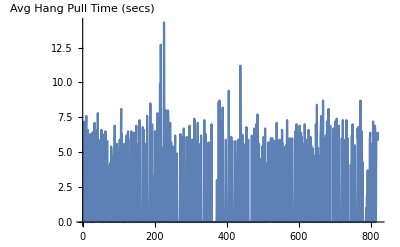

```mathematica
ListLinePlot[teamssummary2017set2[All,27],AxesLabel->{None,HoldForm["Avg Hang Pull Time (secs)"]},Ticks->{None,Automatic}]
```

```mathematica
(* Seasonal Turnovers Trend (Turnovers per Touch)
(as the season progresses is the team experiencing more or less turns each game?) *)
```

```mathematica
(* Step 4 *)
(* Graphics to show how the game is played *)
```

```mathematica
(* Step 5 *)
(* Web Deploy *)

(* Step 6 *)
(* Future Options *)
```